```mathematica
littlewood[n_Integer] := 1 + Tuples[{1,- 1}, n].x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

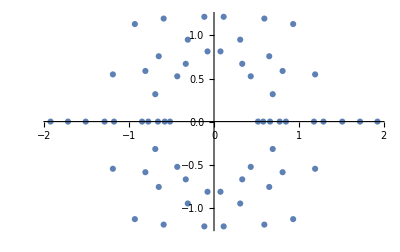

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
showRoots[n_]:=With[{r=NSolveValues[#==0,x]&/@littlewood[n],
s=Which[n<8,Medium,n<14,Small,True,Tiny]},
ComplexListPlot[r,ImageSize->Large,PlotStyle->PointSize@s]]
```

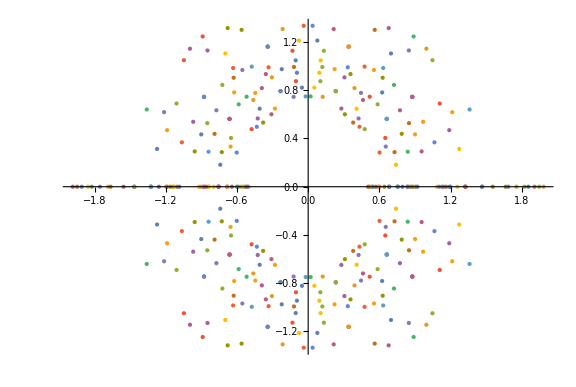

```mathematica
showRoots[6]
```